#### PROJECTILE IN A UNIFORM GRAVITATIONAL FIELD.

```mathematica
(*In this exercise i solve a simple problem in Classical Mechanics. The exercise consists in solve the equation of motion for a particle in two dimensional sistem with a parabolic trajectory. After solved the eq. of motion a plot curves (parametrized in time) {x[t],z[t]} for different final time.The same problem solved also in fuction of the angle.*)


eqns = {x''[t]==0,z''[t]==-g};
initial = {x[0]== 0,x[t1]==x1, z[0]==0,z[t1]==z1};
```

```mathematica
sols = DSolve[Join[eqns,initial],{x[t],z[t]},t]//Flatten
```

{x[t]→(t x1)/t1,z[t]→(-g t^2 t1+g t t1^2+2 t z1)/(2 t1)}

```mathematica
{x[t]->(t x1)/t1,z[t]->(-g t^2 t1+g t t1^2+2 t z1)/(2 t1)}
```

{x[t]→(t x1)/t1,z[t]→(-g t^2 t1+g t t1^2+2 t z1)/(2 t1)}

```mathematica
values={x1->300,z1->0,g->9.8};
points[t_,t1_]= {x[t],z[t]}/.sols/.values
```

{(300 t)/t1,(-9.8 t^2 t1+9.8 t t1^2)/(2 t1)}

```mathematica
pointsplot[t1_]:=
Table[points[t,t1],{t,0,t1,0.7}];

plot1[t1_]:=
ListPlot[pointsplot[t1]//Evaluate,
PlotStyle->{Hue[0.8],PointSize[0.02]},
GridLines->Automatic,
DisplayFunction->Identity]
```

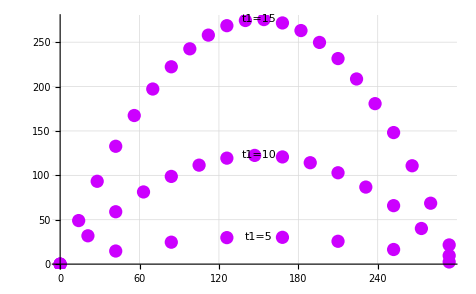

```mathematica
Show[{plot1[5],plot1[10],plot1[15]},
PlotRange->All,
Epilog->{
Text["t1=5",points[5/2,5],
BaseStyle->{FontWeight->"Bold"}],
Text["t1=10",points[10/2,10],
BaseStyle->{FontWeight->"Bold"}],
Text["t1=15",points[15/2,15],
BaseStyle->{FontWeight->"Bold"}]},
DisplayFunction->$DisplayFunction
]
```

```mathematica
initial2 = {x[0]==0,x'[0]==v0 Cos[θ],z[0]==0,z'[0]==v0 Sin[θ]};
sols2= DSolve[Join[eqns,initial2],{x,z},t]//Flatten
```

{x→Function[{t},t v0 Cos[θ]],z→Function[{t},1/2 (-g t^2+2 t v0 Sin[θ])]}

```mathematica
eqn2=z'[t]==0/.sols2
```

1/2 (-2 g t+2 v0 Sin[θ])==0

```mathematica
z'[0]==0/.sols;
tsol=Solve[eqn2,t]//Flatten;
{x[t],z[t]}/.sols2/.tsol//Flatten;
values2={g->9.8,v0->100};
```

```mathematica
points2[t_,θ_]= {x[t],z[t]}/.sols2/. values2
```

{100 t Cos[θ],1/2 (-9.8 t^2+200 t Sin[θ])}

```mathematica
pointsplot2[θ_]= Table[points2[t,θ],{t,0,40,0.55}];
```

```mathematica
plot2[θ_]:=
ListPlot[pointsplot2[θ]//Evaluate,
PlotStyle->{Hue[0.8],PointSize[0.02]},
GridLines->Automatic,
DisplayFunction->Identity];
```

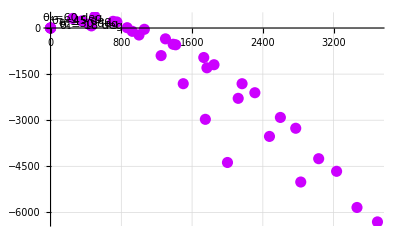

```mathematica
Show[plot2[#]&/@{Pi/8,Pi/6,Pi/4,Pi/3},
PlotRange->All,
Epilog->{
Text["θ_1= 18 deg",points2[5,Pi/8],
BaseStyle->{FontWeight->"Bold"}],
Text["θ_2=30 deg",points2[5,Pi/6],
BaseStyle->{FontWeight->"Bold"}],
Text["θ_3=45 deg",points2[5,Pi/4],
BaseStyle->{FontWeight->"Bold"}],
Text["θ_4=60 deg",points2[5,Pi/3],
BaseStyle->{FontWeight->"Bold"}]
},
DisplayFunction->$DisplayFunction
]
```